# PeterBurbery/AssociationFunctions

Functions for modifying associations

## Paclet

### Paclet Directory

NotebookDirectory[]

### Manifest

"Documentation"

"English"

"Guides"

"AssociationFunctions.nb"Documentation/English/Guides/AssociationFunctions.nb

"ReferencePages"

"Tutorials"

"Kernel"

"AssociationFunctions.wl"Kernel/AssociationFunctions.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

Functions for manipulating and creating associations.

### Details

Additional information about the paclet.

### Main Guide Page

"Documentation/English/Guides/AssociationFunctions.nb"

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[];
```

### Basic Examples

Generate an Association to label the results of different operations on an expression:

```mathematica
AssociationThrough[{f,g},{1,2,3,4}]
```

<|f→f[{1,2,3,4}],g→g[{1,2,3,4}]|>

Perform multiple statistical operations on a single distribution, returning a single expression:

```mathematica
AssociationThrough[{Min,Max,StandardDeviation,GeometricMean},{1,2,3,4}]
```

<|Min→1,Max→4,StandardDeviation→√(5/3),GeometricMean→2^(3/4) 3^(1/4)|>

### Statistical Examples

The keys are cities and the values are the cost of a round trip airplane ticket:

```mathematica
cities=<|"Miami"->230,"San Diego"->651,"New York City"->221,"Chicago"->279,"Seattle"->722,"Salt Lake City"->768,"Boston"->221,"Honolulu"->970,"Denver"->529,"Boulder, Colorado"->529|>;
```

I create a function to compute the geographical coordinates of a place from Wikidata:

```mathematica
WikidataGeoPosition[place_?StringQ]:=First[WikidataData[First[WikidataSearch[place]],ExternalIdentifier["WikidataID","P625",<|"Label"->"coordinate location","Description"->"geocoordinates of the subject. For Earth, please note that only WGS84 coordinating system is supported at the moment"|>]"Wikidata""coordinate location"http://www.wikidata.org/entity/P625]]
```

compute the distances to the cities:

```mathematica
data=AssociationMap[<|"Position"->WikidataGeoPosition[#],"Distance"->GeoDistance[Here,WikidataGeoPosition[#]],"RoundtripTicket"->cities[#]|>&,Keys[cities]]
```

<|Miami→<|Position→GeoPosition[{25.7833,-80.2167}],Distance→1415.68 km,RoundtripTicket→230|>,San Diego→<|Position→GeoPosition[{32.715,-117.163}],Distance→3191.1 km,RoundtripTicket→651|>,New York City→<|Position→GeoPosition[{40.7,-74.}],Distance→768.258 km,RoundtripTicket→221|>,Chicago→<|Position→GeoPosition[{41.85,-87.6501}],Distance→585.534 km,RoundtripTicket→279|>,Seattle→<|Position→GeoPosition[{47.6062,-122.332}],Distance→3367.1 km,RoundtripTicket→722|>,Salt Lake City→<|Position→GeoPosition[{40.75,-111.883}],Distance→2530.98 km,RoundtripTicket→768|>,Boston→<|Position→GeoPosition[{42.3603,-71.0578}],Distance→1060.21 km,RoundtripTicket→221|>,Honolulu→<|Position→GeoPosition[{21.3047,-157.857}],Distance→7331.02 km,RoundtripTicket→970|>,Denver→<|Position→GeoPosition[{39.7392,-104.985}],Distance→1951.33 km,RoundtripTicket→529|>,Boulder, Colorado→<|Position→GeoPosition[{40.0194,-105.293}],Distance→1976.28 km,RoundtripTicket→529|>|>

organize the data for processing:

```mathematica
dataset=Dataset[data]
```

-Graphics-

turn the data into an association:

```mathematica
geoData=AssociationThread[Values@Normal@dataset[All,"Position"],Values@Normal@dataset[All,"RoundtripTicket"]]
```

<|GeoPosition[{25.7833,-80.2167}]→230,GeoPosition[{32.715,-117.163}]→651,GeoPosition[{40.7,-74.}]→221,GeoPosition[{41.85,-87.6501}]→279,GeoPosition[{47.6062,-122.332}]→722,GeoPosition[{40.75,-111.883}]→768,GeoPosition[{42.3603,-71.0578}]→221,GeoPosition[{21.3047,-157.857}]→970,GeoPosition[{39.7392,-104.985}]→529,GeoPosition[{40.0194,-105.293}]→529|>

Make a geo bubble chart for the cost of the round trip ticket and the distance:

```mathematica
Labeled[GeoBubbleChart[AssociationThread[Values@Normal@dataset[All,"Position"],Values@Normal@dataset[All,"RoundtripTicket"]],],"Round trip ticket geo bubble chart"]
```

-Graphics-

```mathematica
Labeled[GeoBubbleChart[AssociationThread[Values@Normal@dataset[All,"Position"],Values@Normal@dataset[All,"Distance"]],],"Distance geobubble chart"]
```

-Graphics-

Make a plot of distance and cost:

```mathematica
AssociationThread[Values@Normal@dataset[All,"Distance"],Values@Normal@dataset[All,"RoundtripTicket"]]
```

<|1415.68 km→230,3191.1 km→651,768.258 km→221,585.534 km→279,3367.1 km→722,2530.98 km→768,1060.21 km→221,7331.02 km→970,1951.33 km→529,1976.28 km→529|>

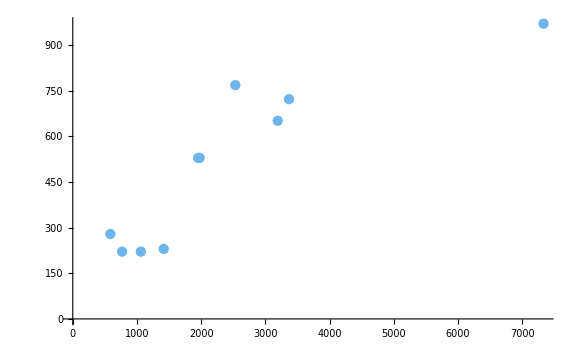
-Graphics-Distance verses cost

```mathematica
Labeled[ListPlot[AssociationThread[Values@Normal@dataset[All,"Distance"],Values@Normal@dataset[All,"RoundtripTicket"]],ImageSize->Large,PlotStyle->"Pastel"],"Distance verses cost"]
```

I think the line starts at 100 and has a slope of 0.15:

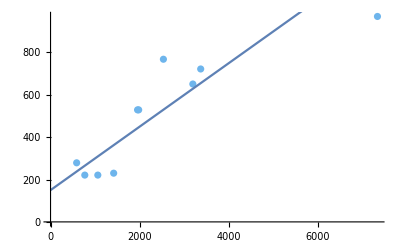

```mathematica
Show[ListPlot[AssociationThread[Values@Normal@dataset[All,"Distance"],Values@Normal@dataset[All,"RoundtripTicket"]],ImageSize->Full,PlotStyle->"Pastel"],Plot[150+0.15x,{x,0,7000}]]
```

```mathematica
CopyToClipboard[Rasterize@Show[ListPlot[AssociationThread[Values@Normal@dataset[All,"Distance"],Values@Normal@dataset[All,"RoundtripTicket"]],ImageSize->Full,PlotStyle->"Pastel"],Plot[150+0.15x,{x,0,7000}]]]
```

Let's test our prediction with linear interpolation:

```mathematica
{Values@Normal@dataset[All,#Distance&],Values@Normal@dataset[All,#RoundtripTicket&]}
```

{{1415.68 km,3191.1 km,768.258 km,585.534 km,3367.1 km,2530.98 km,1060.21 km,7331.02 km,1951.33 km,1976.28 km},{230,651,221,279,722,768,221,970,529,529}}

Calculate the linear interpolation for the data:

```mathematica
linearModelFit=LinearModelFit[Transpose@{Values@Normal@dataset[All,QuantityMagnitude[#Distance]&],Values@Normal@dataset[All,#RoundtripTicket&]},x,x]
```

FittedModel[224.879+0.118756 x]

The correct line of best fit is in green and my guess for the line of best fit is in purple:

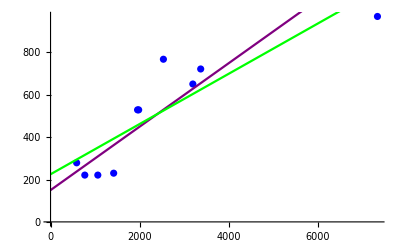

```mathematica
Show[ListPlot[linearModelFit["Data"],ImageSize->Full,PlotStyle->Blue],Plot[150+0.15x,{x,0,7000},PlotStyle->Purple],Plot[linearModelFit[x],{x,0,QuantityMagnitude@Max@dataset[All,#Distance&]},PlotStyle->Green]]
```

### Scope

Give more examples showing the range of features in the paclet:

```mathematica
MyPlot[MyFunction[a,3,4],{a,1,10}]
```

-Graphics-

Use screenshots to show features like notebook styles, palettes and external operations:

```mathematica
ViewWebsite["wolframcloud"]
```

-Graphics-

### Neat Examples

Create a constant association:

```mathematica
Needs["PeterBurbery`AssociationFunctions`"]
```

```mathematica
ConstantAssociation[{a,b,c,d},x]
```

<|a→x,b→x,c→x,d→x|>

Partition an association:

```mathematica
AssociationPartition[AssociationMap[f,ToExpression/@Alphabet[]],2]
```

{<|a→f[a],b→f[b]|>,<|c→f[c],d→f[d]|>,<|e→f[e],f→f[f]|>,<|g→f[g],h→f[h]|>,<|i→f[i],j→f[j]|>,<|k→f[k],l→f[l]|>,<|m→f[m],n→f[n]|>,<|o→f[o],p→f[p]|>,<|q→f[q],r→f[r]|>,<|s→f[s],t→f[t]|>,<|u→f[u],v→f[v]|>,<|w→f[w],x→f[x]|>,<|y→f[y],z→f[z]|>}

Combine partitioning associations with other association operations like AssociationThread:

```mathematica
AssociationThread[Range[3]->(AssociationThread[Range[2]->#]&/@Partition[AssociationThread[Range[2]->#]&/@Partition[AssociationPartition[AssociationMap[f,ToExpression/@Alphabet[][[;;24]]],2],2],2])]
```

<|1→<|1→<|1→<|a→f[a],b→f[b]|>,2→<|c→f[c],d→f[d]|>|>,2→<|1→<|e→f[e],f→f[f]|>,2→<|g→f[g],h→f[h]|>|>|>,2→<|1→<|1→<|i→f[i],j→f[j]|>,2→<|k→f[k],l→f[l]|>|>,2→<|1→<|m→f[m],n→f[n]|>,2→<|o→f[o],p→f[p]|>|>|>,3→<|1→<|1→<|q→f[q],r→f[r]|>,2→<|s→f[s],t→f[t]|>|>,2→<|1→<|u→f[u],v→f[v]|>,2→<|w→f[w],x→f[x]|>|>|>|>

Create a nested dataset:

```mathematica
Dataset[]
```

-Graphics-

Create a large nested association:

```mathematica
AssociationThread[Range[3]->(AssociationThread[Range[2]->#]&/@Partition[AssociationThread[Range[2]->#]&/@Partition[AssociationPartition[AssociationMap[f,Array[a,24]],2],2],2])]
```

<|1→<|1→<|1→<|a[1]→f[a[1]],a[2]→f[a[2]]|>,2→<|a[3]→f[a[3]],a[4]→f[a[4]]|>|>,2→<|1→<|a[5]→f[a[5]],a[6]→f[a[6]]|>,2→<|a[7]→f[a[7]],a[8]→f[a[8]]|>|>|>,2→<|1→<|1→<|a[9]→f[a[9]],a[10]→f[a[10]]|>,2→<|a[11]→f[a[11]],a[12]→f[a[12]]|>|>,2→<|1→<|a[13]→f[a[13]],a[14]→f[a[14]]|>,2→<|a[15]→f[a[15]],a[16]→f[a[16]]|>|>|>,3→<|1→<|1→<|a[17]→f[a[17]],a[18]→f[a[18]]|>,2→<|a[19]→f[a[19]],a[20]→f[a[20]]|>|>,2→<|1→<|a[21]→f[a[21]],a[22]→f[a[22]]|>,2→<|a[23]→f[a[23]],a[24]→f[a[24]]|>|>|>|>

Make a large nested dataset:

```mathematica
Dataset[]
```

-Graphics-

Find all the properties for a linear model fit:

```mathematica
data=Table[k+RandomInteger[{-10,10}],{k,5,100,5}]
```

{2,9,20,28,35,23,45,43,42,45,55,52,69,76,73,79,85,92,96,95}

```mathematica
linearModelFit=LinearModelFit[data,x,x]
```

FittedModel[2.76842+4.80301 x]

```mathematica
PropertiesSummary[linearModelFit]
```

<|AdjustedRSquared→0.96627,AIC→127.496,AICc→128.996,ANOVATable→ | DF | SS | MS | F-Statistic | P-Value
x | 1 | 15340.8 | 15340.8 | 545.296 | 6.53788×10^-15
Error | 18 | 506.394 | 28.133 |  | 
Total | 19 | 15847.2 |  |  | ,ANOVATableDegreesOfFreedom→{1,18,19},ANOVATableEntries→{{1,15340.8,15340.8,545.296,6.53788×10^-15},{18,506.394,28.133},{19,15847.2}},ANOVATableFStatistics→{545.296},ANOVATableMeanSquares→{15340.8,28.133},ANOVATablePValues→{6.53788×10^-15},ANOVATableSumsOfSquares→{15340.8,506.394,15847.2},BasisFunctions→{1,x},BetaDifferences→{{-0.56128,0.480261},{-0.295382,0.245524},{0.218657,-0.175402},{0.426371,-0.327085},{0.530989,-0.384444},{-0.485969,0.325425},{0.418003,-0.250366},{0.0680506,-0.0342516},{-0.124764,0.0457521},{-0.14458,0.0224927},{-0.0105233,-0.00225107},{-0.0998011,-0.102474},{0.0169988,0.0727252},{-0.0138853,0.166334},{0.0164347,-0.0632808},{0.00990919,-0.0266478},{-0.0135981,0.0302517},{-0.0873842,0.172547},{-0.0783055,0.14238},{0.188836,-0.323156}},BestFit→2.76842+4.80301 x,BestFitParameters→{2.76842,4.80301},BIC→130.484,CatcherMatrix→{{0.2,0.184211,0.168421,0.152632,0.136842,0.121053,0.105263,0.0894737,0.0736842,0.0578947,0.0421053,0.0263158,0.0105263,-0.00526316,-0.0210526,-0.0368421,-0.0526316,-0.0684211,-0.0842105,-0.1},{-0.0142857,-0.012782,-0.0112782,-0.00977444,-0.00827068,-0.00676692,-0.00526316,-0.0037594,-0.00225564,-0.00075188,0.00075188,0.00225564,0.0037594,0.00526316,0.00676692,0.00827068,0.00977444,0.0112782,0.012782,0.0142857}},CoefficientOfVariation→0.0997003,CookDistances→{0.154518,0.0453555,0.0254445,0.0930428,0.140041,0.124671,0.103888,0.00389838,0.0169026,0.0333814,0.000359212,0.0747889,0.0171619,0.0502669,0.00556145,0.000788501,0.00086514,0.0246376,0.0155279,0.0729658},CorrelationMatrix→{{1.,-0.876523},{-0.876523,1.}},CovarianceMatrix→{{6.07081,-0.444205},{-0.444205,0.0423053}},CovarianceRatios→{1.17732,1.26223,1.24879,1.06876,0.901014,0.863685,0.854898,1.17561,1.10676,1.02126,1.1788,0.861015,1.12101,1.02738,1.20203,1.23741,1.26279,1.25025,1.30823,1.28065},Data→{2,9,20,28,35,23,45,43,42,45,55,52,69,76,73,79,85,92,96,95},DesignMatrix→{{1.,1.},{1.,2.},{1.,3.},{1.,4.},{1.,5.},{1.,6.},{1.,7.},{1.,8.},{1.,9.},{1.,10.},{1.,11.},{1.,12.},{1.,13.},{1.,14.},{1.,15.},{1.,16.},{1.,17.},{1.,18.},{1.,19.},{1.,20.}},DurbinWatsonD→2.10103,EigenstructureTable→Eigenvalue | Index | x
1. | 1. | 1.,EigenstructureTableEigenvalues→{1.},EigenstructureTableEntries→{{1.,1.,1.}},EigenstructureTableIndexes→{1.},EigenstructureTablePartitions→{{1.}},EstimatedVariance→28.133,FitDifferences→{-0.561807,-0.296689,0.22125,0.437241,0.557002,-0.528951,0.482518,0.0861072,-0.181733,-0.260372,-0.026058,-0.40704,0.182828,0.320567,-0.102858,-0.0386087,0.0404398,0.21765,0.172051,-0.378027},FitResiduals→{-5.57143,-3.37444,2.82256,6.01955,8.21654,-8.58647,8.61053,1.80752,-3.99549,-5.7985,-0.601504,-8.40451,3.79248,5.98947,-1.81353,-0.616541,0.580451,2.77744,1.97444,-3.82857},Function→(2.76842+4.80301 #1&),FVarianceRatios→{1.20242,1.22484,1.20125,1.09802,0.998065,0.969148,0.95796,1.11797,1.08128,1.03703,1.11415,0.953714,1.0917,1.05016,1.14333,1.16963,1.19354,1.20195,1.24696,1.25409},HatDiagonal→{0.185714,0.158647,0.134586,0.113534,0.0954887,0.0804511,0.0684211,0.0593985,0.0533835,0.0503759,0.0503759,0.0533835,0.0593985,0.0684211,0.0804511,0.0954887,0.113534,0.134586,0.158647,0.185714},MeanPredictionBands→{2.76842+4.80301 x-2.10092 √(6.07081-0.88841 x+0.0423053 x^2),2.76842+4.80301 x+2.10092 √(6.07081-0.88841 x+0.0423053 x^2)},MeanPredictionConfidenceIntervals→{{2.76922,12.3736},{7.93597,16.8129},{13.0894,21.2655},{18.2257,25.7352},{23.34,30.2269},{28.4258,34.7472},{33.4746,39.3043},{38.4766,43.9083},{43.4208,48.5702},{48.2974,53.2996},{53.1004,58.1026},{57.8298,62.9792},{62.4917,67.9234},{67.0957,72.9254},{71.6528,77.9742},{76.1731,83.06},{80.6648,88.1743},{85.1345,93.3106},{89.5871,98.464},{94.0264,103.631}},MeanPredictionConfidenceIntervalTable→Observed | Predicted | Standard Error | Confidence Interval
2 | 7.57143 | 2.28576 | {2.76922,12.3736}
9 | 12.3744 | 2.11263 | {7.93597,16.8129}
20 | 17.1774 | 1.94585 | {13.0894,21.2655}
28 | 21.9805 | 1.78719 | {18.2257,25.7352}
35 | 26.7835 | 1.63902 | {23.34,30.2269}
23 | 31.5865 | 1.50444 | {28.4258,34.7472}
45 | 36.3895 | 1.3874 | {33.4746,39.3043}
43 | 41.1925 | 1.29269 | {38.4766,43.9083}
42 | 45.9955 | 1.22549 | {43.4208,48.5702}
45 | 50.7985 | 1.19047 | {48.2974,53.2996}
55 | 55.6015 | 1.19047 | {53.1004,58.1026}
52 | 60.4045 | 1.22549 | {57.8298,62.9792}
69 | 65.2075 | 1.29269 | {62.4917,67.9234}
76 | 70.0105 | 1.3874 | {67.0957,72.9254}
73 | 74.8135 | 1.50444 | {71.6528,77.9742}
79 | 79.6165 | 1.63902 | {76.1731,83.06}
85 | 84.4195 | 1.78719 | {80.6648,88.1743}
92 | 89.2226 | 1.94585 | {85.1345,93.3106}
96 | 94.0256 | 2.11263 | {89.5871,98.464}
95 | 98.8286 | 2.28576 | {94.0264,103.631},MeanPredictionConfidenceIntervalTableEntries→{{2,7.57143,2.28576,{2.76922,12.3736}},{9,12.3744,2.11263,{7.93597,16.8129}},{20,17.1774,1.94585,{13.0894,21.2655}},{28,21.9805,1.78719,{18.2257,25.7352}},{35,26.7835,1.63902,{23.34,30.2269}},{23,31.5865,1.50444,{28.4258,34.7472}},{45,36.3895,1.3874,{33.4746,39.3043}},{43,41.1925,1.29269,{38.4766,43.9083}},{42,45.9955,1.22549,{43.4208,48.5702}},{45,50.7985,1.19047,{48.2974,53.2996}},{55,55.6015,1.19047,{53.1004,58.1026}},{52,60.4045,1.22549,{57.8298,62.9792}},{69,65.2075,1.29269,{62.4917,67.9234}},{76,70.0105,1.3874,{67.0957,72.9254}},{73,74.8135,1.50444,{71.6528,77.9742}},{79,79.6165,1.63902,{76.1731,83.06}},{85,84.4195,1.78719,{80.6648,88.1743}},{92,89.2226,1.94585,{85.1345,93.3106}},{96,94.0256,2.11263,{89.5871,98.464}},{95,98.8286,2.28576,{94.0264,103.631}}},MeanPredictionErrors→{2.28576,2.11263,1.94585,1.78719,1.63902,1.50444,1.3874,1.29269,1.22549,1.19047,1.19047,1.22549,1.29269,1.3874,1.50444,1.63902,1.78719,1.94585,2.11263,2.28576},ParameterConfidenceIntervals→{{-2.40804,7.94488},{4.37088,5.23513}},ParameterConfidenceIntervalTable→ | Estimate | Standard Error | Confidence Interval
1 | 2.76842 | 2.4639 | {-2.40804,7.94488}
x | 4.80301 | 0.205682 | {4.37088,5.23513},ParameterConfidenceIntervalTableEntries→{{2.76842,2.4639,{-2.40804,7.94488}},{4.80301,0.205682,{4.37088,5.23513}}},ParameterConfidenceRegion→FittedModels`ParameterEllipsoid[{2.76842,4.80301},{6.58707,0.263277},{{-0.997325,0.0730924},{-0.0730924,-0.997325}}],ParameterErrors→{2.4639,0.205682},ParameterPValues→{0.275948,6.53788×10^-15},ParameterTable→ | Estimate | Standard Error | t-Statistic | P-Value
1 | 2.76842 | 2.4639 | 1.12359 | 0.275948
x | 4.80301 | 0.205682 | 23.3516 | 6.53788×10^-15,ParameterTableEntries→{{2.76842,2.4639,1.12359,0.275948},{4.80301,0.205682,23.3516,6.53788×10^-15}},ParameterTStatistics→{1.12359,23.3516},PartialSumOfSquares→{15340.8},PredictedResponse→{7.57143,12.3744,17.1774,21.9805,26.7835,31.5865,36.3895,41.1925,45.9955,50.7985,55.6015,60.4045,65.2075,70.0105,74.8135,79.6165,84.4195,89.2226,94.0256,98.8286},Properties→{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors},Response→{2,9,20,28,35,23,45,43,42,45,55,52,69,76,73,79,85,92,96,95},RSquared→0.968045,SequentialSumOfSquares→{15340.8},SingleDeletionVariances→{27.5455,28.9918,29.2464,27.3834,25.3974,25.0715,25.1063,29.5836,28.7959,27.7052,29.7655,25.3985,28.8884,27.5227,29.5775,29.7632,29.7655,29.2635,29.5153,28.729},SinglePredictionBands→{2.76842+4.80301 x-2.10092 √(34.2038-0.88841 x+0.0423053 x^2),2.76842+4.80301 x+2.10092 √(34.2038-0.88841 x+0.0423053 x^2)},SinglePredictionConfidenceIntervals→{{-4.56268,19.7055},{0.379624,24.3692},{5.30783,29.0471},{10.2215,33.7394},{15.1201,38.4468},{20.0035,43.1695},{24.8712,47.9078},{29.7229,52.6621},{34.5585,57.4325},{39.3779,62.2191},{44.1809,67.0221},{48.9675,71.8415},{53.7379,76.6771},{58.4922,81.5288},{63.2305,86.3965},{67.9532,91.2799},{72.6606,96.1785},{77.3529,101.092},{82.0308,106.02},{86.6945,110.963}},SinglePredictionConfidenceIntervalTable→Observed | Predicted | Standard Error | Confidence Interval
2 | 7.57143 | 5.77561 | {-4.56268,19.7055}
9 | 12.3744 | 5.70931 | {0.379624,24.3692}
20 | 17.1774 | 5.64972 | {5.30783,29.0471}
28 | 21.9805 | 5.59706 | {10.2215,33.7394}
35 | 26.7835 | 5.55152 | {15.1201,38.4468}
23 | 31.5865 | 5.51329 | {20.0035,43.1695}
45 | 36.3895 | 5.48251 | {24.8712,47.9078}
43 | 41.1925 | 5.45931 | {29.7229,52.6621}
42 | 45.9955 | 5.44379 | {34.5585,57.4325}
45 | 50.7985 | 5.43601 | {39.3779,62.2191}
55 | 55.6015 | 5.43601 | {44.1809,67.0221}
52 | 60.4045 | 5.44379 | {48.9675,71.8415}
69 | 65.2075 | 5.45931 | {53.7379,76.6771}
76 | 70.0105 | 5.48251 | {58.4922,81.5288}
73 | 74.8135 | 5.51329 | {63.2305,86.3965}
79 | 79.6165 | 5.55152 | {67.9532,91.2799}
85 | 84.4195 | 5.59706 | {72.6606,96.1785}
92 | 89.2226 | 5.64972 | {77.3529,101.092}
96 | 94.0256 | 5.70931 | {82.0308,106.02}
95 | 98.8286 | 5.77561 | {86.6945,110.963},SinglePredictionConfidenceIntervalTableEntries→{{2,7.57143,5.77561,{-4.56268,19.7055}},{9,12.3744,5.70931,{0.379624,24.3692}},{20,17.1774,5.64972,{5.30783,29.0471}},{28,21.9805,5.59706,{10.2215,33.7394}},{35,26.7835,5.55152,{15.1201,38.4468}},{23,31.5865,5.51329,{20.0035,43.1695}},{45,36.3895,5.48251,{24.8712,47.9078}},{43,41.1925,5.45931,{29.7229,52.6621}},{42,45.9955,5.44379,{34.5585,57.4325}},{45,50.7985,5.43601,{39.3779,62.2191}},{55,55.6015,5.43601,{44.1809,67.0221}},{52,60.4045,5.44379,{48.9675,71.8415}},{69,65.2075,5.45931,{53.7379,76.6771}},{76,70.0105,5.48251,{58.4922,81.5288}},{73,74.8135,5.51329,{63.2305,86.3965}},{79,79.6165,5.55152,{67.9532,91.2799}},{85,84.4195,5.59706,{72.6606,96.1785}},{92,89.2226,5.64972,{77.3529,101.092}},{96,94.0256,5.70931,{82.0308,106.02}},{95,98.8286,5.77561,{86.6945,110.963}}},SinglePredictionErrors→{5.77561,5.70931,5.64972,5.59706,5.55152,5.51329,5.48251,5.45931,5.44379,5.43601,5.43601,5.44379,5.45931,5.48251,5.51329,5.55152,5.59706,5.64972,5.70931,5.77561},StandardizedResiduals→{-1.16405,-0.693592,0.572035,1.20538,1.62882,-1.68818,1.68195,0.351376,-0.774239,-1.12184,-0.116374,-1.62861,0.737246,1.16996,-0.356558,-0.122221,0.116232,0.562892,0.405832,-0.799909},StudentizedResiduals→{-1.17639,-0.683242,0.561041,1.22177,1.7143,-1.78828,1.78044,0.342653,-0.765275,-1.13047,-0.113137,-1.71404,0.727543,1.18286,-0.347742,-0.118827,0.113,0.551912,0.396214,-0.791568},VarianceInflationFactors→{0.,1.}|>

Find all the values for a country:

```mathematica
PropertiesSummary[]
```

Lookup::invrl: The argument EntityValue[False,False,False] is not a valid Association or a list of rules.

Pick::incomp: Expressions {EntityProperty[EntityType,LabelPlural]} and {!Lookup[EntityFramework`Caching`Private`cacheData$780524,EntityProperty[EntityType,LabelPlural],False]} have incompatible shapes.

Lookup::invrl: The argument EntityValue[False,False,False] is not a valid Association or a list of rules.

Pick::incomp: Expressions {EntityProperty[EntityType,LabelPlural]} and {!Lookup[EntityFramework`Caching`Private`cacheData$785835,EntityProperty[EntityType,LabelPlural],False]} have incompatible shapes.

## Source & Additional Information

### Creator

Peter Cullen Burbery

### Source Control Repository

https://github.com/PeterCullenBurbery/association-functions

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

associations

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

### Disclosures

DisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more informationLocal files

DisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more informationWolfram account

DisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more informationExternal services

DisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates, modifies or deletes symbols outside of the Publisher`PacletBaseName` context
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more informationWL system configuration

DisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more informationOS configuration

DisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more informationLocal system interactions

DisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more informationOther

## Author Notes

Additional information about limitations, issues, etc.